# Release Summary

## v0.11

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

This major release significantly extends QuESTlink’s analytic processing of symbolic circuits.
It introduces new symbols and functions:
    • Matr
    • GetCircuitInverse
    • SimplifyCircuit
    • GetKnownCircuit
    • CalcCircuitMatrix
    • GetCircuitGeneralised
    • GetCircuitSuperoperator
in addition to some other changes.

## New features

### Matr

The new circuit symbol Matr works just like U except it does not enforce unitarity. This is convenient to effect general non-unitary operations, or operators which are only approximtely unitary due to numerical imprecision

```mathematica
?Matr
```

```mathematica
circ = Circuit[ Subscript[Matr, 0][({{1, 2}, {3, 4}})] Subscript[C, 0,1][ Subscript[Matr, 2,3][({{.1, 0, 0, ⅇ^(.2 ⅈ)}, {0, ⅈ, 0, 0}, {-2, 0, 0, 0}, {0, 0, π, 1}})]]];
```

```mathematica
DrawCircuit[circ]
```

-Graphics-

```mathematica
CalcCircuitMatrix[circ][[;;8,;;8]] // MatrixForm
```

(1.+0. ⅈ | 2.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
3.+0. ⅈ | 4.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 2.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.3+0. ⅈ | 0.4+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 2.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 3.+0. ⅈ | 4.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ | 2.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+3. ⅈ | 0.+4. ⅈ)

```mathematica
InitPlusState @ CreateQureg[4];
ApplyCircuit[%, circ];
GetQuregMatrix[%%] // MatrixForm
```

(0.75+0. ⅈ
1.75+0. ⅈ
0.75+0. ⅈ
1.89012+0.347671 ⅈ
0.75+0. ⅈ
1.75+0. ⅈ
0.75+0. ⅈ
0.+1.75 ⅈ
0.75+0. ⅈ
1.75+0. ⅈ
0.75+0. ⅈ
-3.5+0. ⅈ
0.75+0. ⅈ
1.75+0. ⅈ
0.75+0. ⅈ
7.24779+0. ⅈ)

### GetCircuitInverse

GetCircuitInverse[circ] returns a symbolic circuit description of the inverse of the input circuit.

```mathematica
?GetCircuitInverse
```

For instance, this non-trivial input circuit...

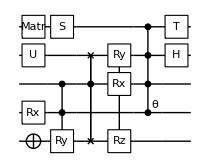

```mathematica
circ = Circuit[ Subscript[X, 0] Subscript[Rx, 1][a] Subscript[C, 1,2][Subscript[Ry, 0][b]]  Subscript[U, 3][({{a, b}, {c, d}})]  Subscript[Matr, 4][({{a, b}, {c, d}})] G[e] Subscript[C, 2][Subscript[SWAP, 0,3]] R[f,Subscript[X, 2] Subscript[Y, 3] Subscript[Z, 0]] Subscript[S, 4] Subscript[C, 4][Subscript[Ph, 3,2,1][g]] Subscript[T, 4] Subscript[H, 3]];

DrawCircuit[circ]
```

is inverted to

```mathematica
inv = GetCircuitInverse[circ]
```

{H_3,Ph_4[-π/4],C_4[Ph_(3,2,1)[-g]],Ph_4[-π/2],R[-f,X_2 Y_3 Z_0],C_2[SWAP_(0,3)],G[-e],Matr_4[{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}],U_3[{{Conjugate[a],Conjugate[c]},{Conjugate[b],Conjugate[d]}}],C_(1,2)[Ry_0[-b]],Rx_1[-a],X_0}

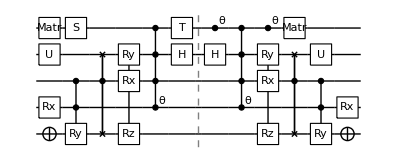

```mathematica
DrawCircuit[{circ, inv}]
```

Beware that not every gate has an inverse.

```mathematica
GetCircuitInverse @ Circuit[Subscript[M, 0]]
```

GetCircuitInverse::error: Could not determine the inverse of gate M_0.

$Failed

### SimplifyCircuit

SimplifyCircuit[circ] performs basic but comprehensive simplification of the circuit, useful as a pre-step before advanced topological or approximate simplification. SimplifyCircuit will...
    • remove adjacent idempotent operations
    • sort gate qubit indices, even if this requires adjusting the gate arguments
    • combine arguments of adjacent parameterised gates
    • multiply matrices of adjacent unitaries
    • merge global phases
    • merge adjacent Pauli operators, and with Pauli rotations
    • remove zero-parameter and identity gates
    • mod arguments of rotation gates to within their periods
    • simplify single-target Pauli gadgets to rotations
    • replace special-param rotation gates with global phases

```mathematica
?SimplifyCircuit
```

```mathematica
SimplifyCircuit @ Circuit[ Subscript[Ph, 0,1][x] Subscript[C, 1][Subscript[Ph, 0][y]] Subscript[C, 0][Subscript[S, 1]] Subscript[C, 1][Subscript[T, 0]] ]
```

{Ph_(0,1)[(3 π)/4+x+y]}

```mathematica
SimplifyCircuit @ Circuit[
	Subscript[hi, 0] Subscript[SWAP, 1,2] Subscript[H, 2] Subscript[H, 0] Subscript[X, 1] Subscript[Y, 2] Subscript[Z, 3] Subscript[X, 1] Subscript[Y, 2] Subscript[H, 2] Subscript[Z, 3] Subscript[C, 1][Subscript[X, 0]]Subscript[C, 2][Subscript[Y, 3]] Subscript[C, 2][Subscript[Y, 3]]Subscript[C, 1][Subscript[X, 0]] Subscript[H, 0] Subscript[SWAP, 2,1]]
```

{hi_0}

Expect the number and nature of these simplifications to grow and improve as QuESTlink matures

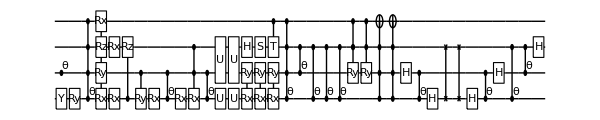

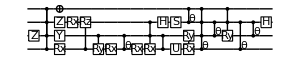

```mathematica
circ = Circuit[Subscript[Y, 0] Subscript[Ry, 0][π] Subscript[Ph, 1][π] Subscript[Ph, 0,1,2,3][π] R[π,Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2] Subscript[X, 3]] R[eh, Subscript[X, 0]] Subscript[Rx, 2][-π]  Subscript[C, 0][Subscript[Rz, 2][π]] Subscript[C, 1][R[ϕ,Subscript[Y, 0]]] Subscript[Rx, 0][a] Subscript[Ph, 0,1][13] Subscript[Rx, 0][11π] G[x] Subscript[C, 2,1][Subscript[Rx, 0][11π]] Subscript[Ph, 1,0][-π] Subscript[U, 2,1][({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})] Subscript[U, 2,1][Inverse@({{a, b, c, d}, {e, f, g, h}, {i, j, k, l}, {m, n, o, p}})]  Subscript[U, 0][{{a,b},{c,d}}] G[z] Subscript[U, 0][({{e, f}, {g, h}})] Subscript[H, 2] R[3,Subscript[X, 0] Subscript[Y, 1]] R[200,Subscript[X, 0] Subscript[Y, 1]] R[-5,Subscript[X, 0] Subscript[Y, 1]]  Subscript[S, 2] Subscript[C, 3][Subscript[T, 2]] Subscript[C, 3,2][Subscript[Ph, 1,0][x]] Subscript[Ph, 2,1][π/2] Subscript[Ph, 2,0][π/4] Subscript[Ph, 0,2][π/4] Subscript[C, 2][Subscript[Ph, 0][-π/2]] Subscript[C, 3,2,2][Subscript[Ry, 1][e]] Subscript[C, {3,2}][Subscript[Ry, 1][e]] Subscript[C, 0,2,1][Subscript[X, 3]] Subscript[C, 0,1,2][Subscript[X, 3]] Subscript[H, 1] Subscript[Ph, 1,0][π/2] Subscript[H, 0] Subscript[SWAP, 0,2] Subscript[SWAP, 0,2] Subscript[H, 0] G[eh] Subscript[Ph, 1,0][-π/2] Subscript[H, 1] Subscript[Ph, 2,0][-π/4] Subscript[Ph, 2,1][-π/2] Subscript[H, 2]];

DrawCircuit[circ, ImageSize -> 600]
DrawCircuit[SimplifyCircuit@circ, ImageSize -> 300]
```

### GetKnownCircuit

GetKnownCircuit[] can dynamically generate canonical quantum circuits.

```mathematica
?GetKnownCircuit
```

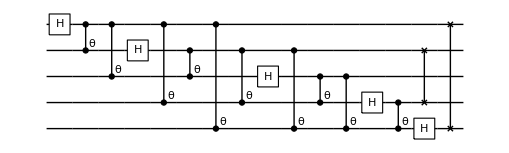

```mathematica
DrawCircuit @ GetKnownCircuit["QFT", 5]
```

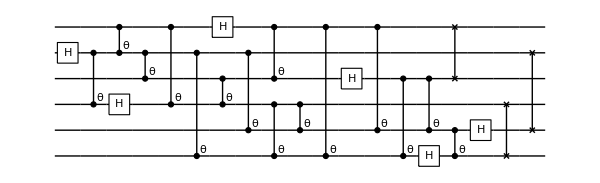

```mathematica
DrawCircuit @ GetKnownCircuit["QFT", {1,0,3,5,2,4}]
```

{R[(a t)/4,X_0],R[(c t)/4,X_2 Z_0],R[(b t)/4,Y_0 Y_1 Z_2],R[(b t)/4,Y_0 Y_1 Z_2],R[(c t)/4,X_2 Z_0],R[(a t)/4,X_0],R[(a t)/4,X_0],R[(c t)/4,X_2 Z_0],R[(b t)/4,Y_0 Y_1 Z_2],R[(b t)/4,Y_0 Y_1 Z_2],R[(c t)/4,X_2 Z_0],R[(a t)/4,X_0]}

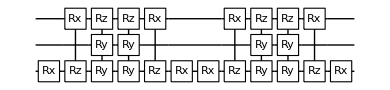

```mathematica
GetKnownCircuit["Trotter", a Subscript[X, 0]+b Subscript[Y, 0] Subscript[Y, 1] Subscript[Z, 2] + c Subscript[Z, 0] Subscript[X, 2], 2, 2, t]
DrawCircuit[%]
```

We expect this family of circuits to quickly grow and include canonical variational circuits.

### CalcCircuitMatrix

CalcCircuitMatrix[] can now analytically evaluate channels!

```mathematica
?CalcCircuitMatrix
```

```mathematica
CalcCircuitMatrix @ Circuit[ Subscript[Deph, 0][λ] ]
```

{{√(1-λ) Conjugate[√(1-λ)]+√λ Conjugate[√λ],0,0,0},{0,√(1-λ) Conjugate[√(1-λ)]-√λ Conjugate[√λ],0,0},{0,0,√(1-λ) Conjugate[√(1-λ)]-√λ Conjugate[√λ],0},{0,0,0,√(1-λ) Conjugate[√(1-λ)]+√λ Conjugate[√λ]}}

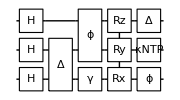

```mathematica
circ = Circuit[Subscript[H, 0] Subscript[H, 1] Subscript[H, 2] Subscript[Depol, 0,1][a] Subscript[Deph, 1,2][b] Subscript[Damp, 0][c]R[2,Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2]] Subscript[KrausNonTP, 1][{({{a, b}, {c, d}}), ({{b, c}, {c, a}})}] Subscript[Deph, 0][a]Subscript[Depol, 2][b]];
DrawCircuit[circ]
```

```mathematica
matr = CalcCircuitMatrix[circ /. {a->.1,b->.2,c->.3,d->.4}];
N @ matr⟦1,1⟧
```

0.0218241+0. ⅈ

The result is a superoperator matrix which can be multiplied upon a column-flattened density matrix. The latter is obtained by Flatten @ Transpose @ matrix

```mathematica
ρ = InitPlusState @ CreateDensityQureg[3];
ρv = Flatten @ Transpose @GetQuregMatrix[ρ];
σv = matr . ρv // Chop
```

{0.0149415,0.0225279,0.0243866,0.016442,0,0,0,0,0.0225279,0.0759462,0.0426938,0.065502,0,0,0,0,0.0243866,0.0426938,0.0477619,0.0422399,0,0,0,0,0.016442,0.065502,0.0422399,0.102294,0,0,0,0,0,0,0,0,0.00229868,0.00346584,0.00375179,0.00252954,0,0,0,0,0.00346584,0.011684,0.00656828,0.0100772,0,0,0,0,0.00375179,0.00656828,0.00734799,0.00649845,0,0,0,0,0.00252954,0.0100772,0.00649845,0.0157375}

It is trivial to reformat this back to a matrix for comparison to QuESTlink’s numerical methods.

```mathematica
ApplyCircuit[ρ, circ /. {a->.1,b->.2,c->.3,d->.4}];
GetQuregMatrix[ρ] - Transpose @ ArrayReshape[σv, {2^3,2^3}] // Chop
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

### GetCircuitGeneralised

GetCircuitGeneralised[circ] produces an equivalent circuit composed only of general operators. This is likely only useful as a subroutine in user-implemented recompilation schemes.

```mathematica
?GetCircuitGeneralised
```

```mathematica
GetCircuitGeneralised @ Circuit[Subscript[X, 0] Subscript[Y, 1] Subscript[C, 0][Subscript[Z, 1]]]
```

{U_0[{{0,1},{1,0}}],U_1[{{0,-ⅈ},{ⅈ,0}}],U_(1,0)[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}}]}

```mathematica
GetCircuitGeneralised @ Circuit[Subscript[Depol, 0][a]]
```

{Kraus_0[{{{√(1-a),0},{0,√(1-a)}},{{0,(√a)/(√3)},{(√a)/(√3),0}},{{0,-(ⅈ √a)/(√3)},{(ⅈ √a)/(√3),0}},{{(√a)/(√3),0},{0,-(√a)/(√3)}}}]}

### GetCircuitSuperoperator

GetCircuitSuperoperator[circ] produces a Choi--Jamiolkowski superoperator of the input circuit. This will again be most useful for user subroutines.

```mathematica
?GetCircuitSuperoperator
```

```mathematica
GetCircuitSuperoperator @ Circuit[Subscript[X, 0]]
```

{X_0,X_1}

```mathematica
GetCircuitSuperoperator @ Circuit[Subscript[Rx, 1][a]]
```

{Rx_1[a],Rx_3[-a]}

```mathematica
GetCircuitSuperoperator @ Circuit[Subscript[Depol, 1][a]]
```

{Matr_(1,3)[{{√(1-a) Conjugate[√(1-a)]+1/3 √a Conjugate[√a],0,0,2/3 √a Conjugate[√a]},{0,√(1-a) Conjugate[√(1-a)]-1/3 √a Conjugate[√a],0,0},{0,0,√(1-a) Conjugate[√(1-a)]-1/3 √a Conjugate[√a],0},{2/3 √a Conjugate[√a],0,0,√(1-a) Conjugate[√(1-a)]+1/3 √a Conjugate[√a]}}]}

## Changes

### Gate symbols are now protected

You’ll never accidentally override them again!

```mathematica
?C
```

```mathematica
C = 2;
```

Set::wrsym: Symbol C is Protected.

### CalcCircuitMatrix will report unrecognised gates

```mathematica
CalcCircuitMatrix @ Circuit[Subscript[X, 0] Subscript[Y, 1] Subscript[Shplee, 2]]
```

CalcCircuitMatrix::error: Circuit contained an unrecognised or unsupported gate: Shplee_2

$Failed

### Pauli Hamiltonians will ignore zero scalars

Previously, functions like ApplyPauliSum, CalcExpecPauliSum and CalcPauliSumMatrix would report a “stand-alone scalar” error when they contained a numerical zero, 0.`. Now, this innocuous term often resulting from SimplifyPaulis will be ignored

```mathematica
h = Subscript[X, 0] Subscript[Y, 1] Subscript[Z, 2] + 0.;
{ψ,ϕ} = InitPlusState /@ CreateQuregs[3,2];
CalcExpecPauliSum[ψ,h, ϕ]
```

0.